```mathematica
ResourceFunction["MaTeXInstall"][]
<<MaTeX`
chart2 =Plot3D[2*Sin[Pi*x/10]^2Sin[Pi*y/10]^2,{x,0,10},{y,0,10},BoxStyle-> Directive[Dotted, Gray], Axes->{True, True, True}]
```

Paclet[MaTeX,1.7.8,<>]

-Graphics3D-

```mathematica
Plot3D[-2(Cos[x] + Cos[y]),{x,-Pi, Pi}, {y, -Pi, Pi},BoxStyle-> Directive[Dotted, Gray], Axes->{True, True, True}]
```

-Graphics3D-

```mathematica
textStyle={FontFamily->"Latin Modern Roman",FontSize->12};
u = Plot3D[-2 (Cos[x]+Cos[y]),{x,-π,π},{y,-π,π},PlotTheme->Automatic,BoxStyle->Directive[Dashing[{0,Small}],GrayLevel[0.5]],Axes->{True,True,True},ColorFunction->"Rainbow",  BaseStyle->textStyle, LabelStyle -> Black, AxesStyle->textStyle, ImagePadding->{{45,45},{45,45}}, AxesLabel-> {"x","y", "z"}]
```

-Graphics3D-

```mathematica
-Graphics3D-
v= Plot3D[1/2,{x,-π,π},{y,-π,π}, Boxed -> False,Axes -> None, ColorFunction->"BlueGreenYellow"]
Show[v, u]
```

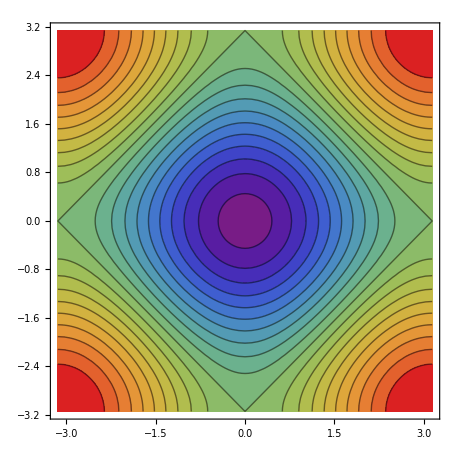

28.3465

-Graphics-

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->11};
f = ContourPlot[-2(Cos[ x]+Cos[y]),{x,-Pi,Pi},{y,-Pi,Pi}, Contours -> 20,Axes -> True, AxesLabel->MaTeX@{"k_x", "k_y", "z"},ImagePadding->{{45,45},{45,45}}, ColorFunction -> "Rainbow" ,Frame -> True, BaseStyle->texStyle, LabelStyle -> Black]
cm=72/2.54
image = Rasterize[Show[f,ImageSize->10cm],"Image",ImageResolution->1000]
```

```mathematica
Export["Dispersion_relation2d_Top.pdf", Show[image, ImageSize -> 10 cm]]
```

Dispersion_relation2d_Top.pdf

```mathematica
SystemOpen["Dispersion_relation2d_Top.pdf"]
```

```mathematica
g = Manipulate[
If[how2D,ContourPlot,DensityPlot,Plot3D]@@{{##,PlotPoints->5},{##,PlotPoints->15},{##,PlotPoints->20},{##,ImageSize->{400,400}}}⟦quality⟧&[
 If[SqrOrLin,x^2+y^2,Abs[√(x^2+y^2)],-2(Cos[ x]+Cos[y])],{x,-Pi,Pi},{y,-Pi,Pi},If[how2D,Contours->20,PlotRange->All,Contours->5],
BoxRatios->If[how2D,Automatic,Automatic,{1,1,1}],If[how2D,Frame->box,Frame->box,Boxed->box],RegionFunction->cut3D,Mesh->mesh,MeshStyle->Directive[Opacity[0.8],Gray],ImageSize->{380,380},BoundaryStyle->{Thick,Gray},ColorFunction->cf,Axes->axes, Ticks -> {{-Pi, 0, Pi},{-Pi, 0, Pi},{-Pi, 0, Pi}},
AxesLabel->{Subscript[k, x] a,Subscript[k, y] a,Row[{Subscript[Style["E",Italic], k],"(eV)"}]},LabelStyle->Directive[Bold,13,Gray],If[how2D,PlotRange->All,PlotRange->All,ViewPoint->vp],MeshFunctions->{#3 &},ImagePadding->{{25,45},{25,45}}],
{{extendBZ,1,"extend BZ"},1,4,1,ControlType->Setter},Delimiter,
Grid[{{  Column[{
Control[{{mesh,False,"show mesh"},{False,40},ControlType->Checkbox}], 
Control[{{box,True,"  show box"},{False,True},ControlType->Checkbox}]    }],"",
Column[{
Control[{{axes,False," show axes"},{False,True},ControlType->Checkbox}],
Control[{{cut3D,True,"cut segment in BZ"},{True,If[how2D,True,True,Function[{x,y},x<0||y>0]]},ControlType->Checkbox}]
   }] }}],
{{quality,2,"quality"},{1->"low",2->"medium",3->"high"}}, {{cf,"Rainbow","colors"},{Automatic->"Automatic","Rainbow"->"Rainbow","DarkRainbow"->"DarkRainbow",Hue->"Hue","CMYKColors"->"CMYKColors","ThermometerColors"->"ThermometerColors","TemperatureMap"->"TemperatureMap","LightTemperatureMap"->"LightTemperatureMap","SouthwestColors"->"SouthwestColors","BlueGreenYellow"->"BlueGreenYellow","LightTerrain"->"LightTerrain","SandyTerrain"->"SandyTerrain","IslandColors"->"IslandColors","Pastel"->"Pastel","PearlColors"->"PearlColors","RedBlueTones"->"RedBlueTones","LakeColors"->"LakeColors","FallColors"->"FallColors","RoseColors"->"RoseColors","WatermelonColors"->"WatermelonColors","GrayYellowTones"->"GrayYellowTones","GreenBrownTerrain"->"GreenBrownTerrain","GrayTones"->"GrayTones"}},Delimiter,
 {{how2D,True,"plot "},{True->"contour",False->"density",Plot3D->"pseudo3D"},ControlType->SetterBar},
{{vp,{1.3,-2.4,2},"3D view"},{{1.3,-2.4,2}->"default",Above->"above",Front->"front"},Enabled:>how2D==Plot3D},Delimiter,
Style["for comparison:",Bold],
 {{SqrOrLin,None,""},{None->"lattice",True->"square",False->"linear"},ControlType->SetterBar},
Style["lattice → lattice electron dispersion",Bold,Gray],
Style["square→ free electron dispersion",Bold,Gray],
Style["linear → Dirac-electron dispersion",Bold,Gray],ControlPlacement->Left,TrackedSymbols->True]
```

```mathematica
Export["Dispersion_relation2d_Top.pdf", g]
```

Dispersion_relation2d_Top.pdf

```mathematica
SystemOpen["Dispersion_relation2d_Top.pdf"]
```

```mathematica
SystemOpen["Dispersion_relation2d_Top.pdf"]
```

```mathematica
h=-2(Cos[x]+Cos[y]);
g=0;
h =ContourPlot3D[{z==0},{x,-Pi,Pi},{y,-Pi,Pi},{z,0,1},MeshFunctions->{Function[{x,y,z,f},h-g]},MeshStyle->{{Thick,Blue}},Mesh->{{0}},ContourStyle->Directive[Orange,Opacity[0],Specularity[White,30]]]
t =Show[u, h, ImageSize -> Large]
Export["Dispersion_relation2d.pdf", t]
```

-Graphics3D-

-Graphics3D-

Dispersion_relation2d.pdf

```mathematica
"Dispersion_relation2d.pdf"
```

Dispersion_relation2d.pdf

```mathematica
Show[t,ImageSize->Large]
```

-Graphics3D-

```mathematica
Export["/Users/fabianjaeger/Desktop/Bachelor Thesis/Bachelor_Thesis/Dispersion_relation2d.pdf",%139,"PDF"]
```

/Users/fabianjaeger/Desktop/Bachelor Thesis/Bachelor_Thesis/Dispersion_relation2d.pdf

-Graphics3D-